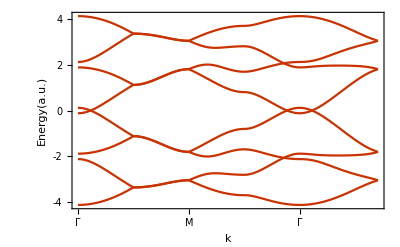

```mathematica
(*Define Academic Theme*)Themes`ThemeRules;
Begin["System`PlotThemeDump`"];
resolvePlotTheme["Academic",def:_String]:=Themes`SetWeight[Join[resolvePlotTheme["AcademicFrame",def],resolvePlotTheme["Figure",def],resolvePlotTheme["HeavyLines",def],resolvePlotTheme["VividColor",def],resolvePlotTheme["SmallOpenMarkers",def]],Themes`$DesignWeight];
resolvePlotTheme["AcademicFrame",def:_String]:=Themes`SetWeight[Join[{Axes->False,Frame->True},resolvePlotTheme["AcademicFrame2D",def]],$ComponentWeight];
resolvePlotTheme["AcademicFrame",def:"PairedBarChart"|"PairedHistogram"]:=Themes`SetWeight[Join[{Axes->True,Frame->True},resolvePlotTheme["AcademicFrame2D",def]],$ComponentWeight];
resolvePlotTheme["AcademicFrame",def:"ArrayPlot"|"MatrixPlot"]:=Themes`SetWeight[Join[{MeshStyle->Directive[AbsoluteThickness[0.5],Opacity[0.25]]},resolvePlotTheme["AcademicFrame2D",def]],$ComponentWeight];
resolvePlotTheme["AcademicFrame",def:"BarChart"|"PieChart"|"RectangleChart"|"SectorChart"|"CandlestickChart"|"KagiChart"|"LineBreakChart"|"PointFigureChart"|"RenkoChart"|"InteractiveTradingChart"|"TradingChart"]:=resolvePlotTheme["AcademicFrame2D",def];
resolvePlotTheme["AcademicFrame",def:_String/;StringMatchQ[def,___~~"3D"]]:=Themes`SetWeight[Join[{Axes->True,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back}},resolvePlotTheme["AcademicFrame3D",def]],$ComponentWeight];
resolvePlotTheme["AcademicFrame","ChromaticityPlot3D"]:=Themes`SetWeight[Join[{Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},Boxed->{Left,Top,Front}},resolvePlotTheme["AcademicFrame3D","ChromaticityPlot3D"]],$ComponentWeight];
resolvePlotTheme["AcademicFrame",def:"BarChart3D"|"PieChart3D"|"RectangleChart3D"|"SectorChart3D"]:=resolvePlotTheme["AcademicFrame3D",def];
resolvePlotTheme["AcademicFrame2D",_]:=Themes`SetWeight[{AxesStyle->Directive[AbsoluteThickness[1],monoColor,FontSize->14],FrameStyle->Directive[AbsoluteThickness[1],monoColor,FontSize->14],TicksStyle->Directive[monoColor,FontSize->12],FrameTicksStyle->Directive[monoColor,FontSize->12],GridLinesStyle->Directive[AbsoluteThickness[0.5],Opacity[0.5]]},$ComponentWeight];
resolvePlotTheme["AcademicFrame3D",_]:=Themes`SetWeight[{AxesStyle->Directive[AbsoluteThickness[1],monoColor,FontSize->14],TicksStyle->Directive[monoColor,FontSize->12],BoxStyle->monoColor},$ComponentWeight];
resolvePlotTheme["Figure",def:_String]:=Themes`SetWeight[{ImageSize->{{180},{180}},LabelStyle->Directive[monoColor,FontSize->12]},Themes`$SizeWeight];
resolvePlotTheme["Figure","ArrayPlot"|"MatrixPlot"]:=Themes`SetWeight[{ImageSize->{{140},{140}},LabelStyle->Directive[monoColor,FontSize->12]},Themes`$SizeWeight];
resolvePlotTheme["Figure",def:_String/;StringMatchQ[def,___~~"3D"]]:=Themes`SetWeight[{ImageSize->{{200},{200}},LabelStyle->Directive[monoColor,FontSize->12]},Themes`$SizeWeight];
resolvePlotTheme["VividColor",def:_String]:=Module[{},$ThemeColorIndexed=112;$ThemeColorDensity="ThermometerColors";$ThemeColorArrayPlot={GrayLevel[0],GrayLevel[1]};$ThemeColorDensity3D="ThermometerColors";$ThemeColorVectorDensity="VibrantColorVectorDensityGradient";$ThemeColorFinancial={RGBColor[0.,0.596078,0.109804],RGBColor[0.790588,0.201176,0.]};$ThemeColorGradient={RGBColor[0.790588,0.201176,0.],RGBColor[0.567426,0.32317,0.729831],RGBColor[0.192157,0.388235,0.807843],RGBColor[0.,0.596078,0.109804],RGBColor[1.,0.607843,0.]};$ThemeColorMatrix={{0,RGBColor[0.12810466666666667,0.25882333333333335,0.538562]},{0.1,RGBColor[0.192157,0.388235,0.807843]},{0.499999,RGBColor[0.8384314,0.8776470000000001,0.9615686]},{0.5,RGBColor[{1,1,1}]},{0.500001,RGBColor[0.9581176,0.8402352000000001,0.8]},{0.9,RGBColor[0.790588,0.201176,0.]},{1,RGBColor[0.5270586666666667,0.13411733333333334,0.]}};$ThemeColorFractal="VibrantColorFractalGradient";$ThemeColorWavelet={RGBColor[0.0621178,0.273882,0.727059],RGBColor[0.790588,0.201176,0.],RGBColor[1.,0.607843,0.],RGBColor[1.,1.,1.]};
resolvePlotTheme["ColorStyle",def]];
resolvePlotTheme["SmallOpenMarkers",def:_String]:={};
resolvePlotTheme["SmallOpenMarkers","DateListLogPlot"|"DateListPlot"|"DiscretePlot"|"ListCurvePathPlot"|"ListLinePlot"|"ListLogLinearPlot"|"ListLogLogPlot"|"ListLogPlot"|"ListPlot"]:=Themes`SetWeight[{PlotMarkers->Module[{s1=2.,s2=1.8,s3=2.5,s4=1.3,thickness=1.5},{Graphics[{{White,Disk[{0,0},Offset[{s1,s1}]]},{AbsoluteThickness[thickness],Dashing[{}],Circle[{0,0},Offset[{s1,s1}]]}}],Graphics[{{White,Polygon[{Offset[{0,2*s4}],Offset[s4*{-Sqrt[3],-1}],Offset[s4*{Sqrt[3],-1}]}]},{AbsoluteThickness[thickness],Dashing[{}],JoinedCurve[Line[{Offset[{0,2*s4}],Offset[s4*{-Sqrt[3],-1}],Offset[s4*{Sqrt[3],-1}],Offset[{0,2*s4}]}],CurveClosed->True]}}],Graphics[{{White,Polygon[{Offset[{0,s3}],Offset[{s3,0}],Offset[{0,-s3}],Offset[{-s3,0}]}]},{AbsoluteThickness[thickness],Dashing[{}],Line[{Offset[{0,s3}],Offset[{s3,0}],Offset[{0,-s3}],Offset[{-s3,0}],Offset[{0,s3}]}]}}],Graphics[{{White,Polygon[{Offset[{-s2,-s2}],Offset[{s2,-s2}],Offset[{s2,s2}],Offset[{-s2,s2}],Offset[{-s2,-s2}]}]},{AbsoluteThickness[thickness],Dashing[{}],Line[{Offset[{-s2,-s2}],Offset[{s2,-s2}],Offset[{s2,s2}],Offset[{-s2,s2}],Offset[{-s2,-s2}]}]}}],Graphics[{{White,Polygon[{Offset[{0,-2*s4}],Offset[s4*{-Sqrt[3],1}],Offset[s4*{Sqrt[3],1}]}]},{AbsoluteThickness[thickness],Dashing[{}],JoinedCurve[Line[{Offset[{0,-2*s4}],Offset[s4*{-Sqrt[3],1}],Offset[s4*{Sqrt[3],1}],Offset[{0,-2*s4}]}],CurveClosed->True]}}]}]},$ComponentWeight]
End[];
$PlotTheme="Academic";
k1f[s_]:=(s-π)HeavisideTheta[π-s]+(s-2π)*HeavisideTheta[2π-s]+(3π-s)*HeavisideTheta[3π-s]+1/(√2)(4π-s)*HeavisideTheta[4π-s]+1/(√2)(s-4π)HeavisideTheta[(4+√2)π-s];
k2f[s_]:=(π-s)HeavisideTheta[π-s]+(s-2π)HeavisideTheta[2π-s]+(s-3π)HeavisideTheta[3π-s]+((4+2 √2)π-(1+1/(√2))s)HeavisideTheta[4π-s]+1/(√2)(s-4π)HeavisideTheta[(4+√2)π-s];
H[t1_,t2_,δ_,k1_,k2_]:={{0,t1,0,0,0,ⅇ^(ⅈ k2) t1,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}
signconfig1 =  {-1,-1,-1,1,1,1,1,-1};
With[{t1=1.0,t2=2.0,δ1=0.5},Plot[Sort[Eigenvalues[N[H[t1,t2,δ1,k1f[s*π],k2f[s*π]]+DiagonalMatrix[δ1*signconfig1]]]],{s,0,4+√2},Frame->True,FrameTicks->{{{-4,-2,0,2,4},None},{{0,Γ},{1,Χ},{2,Μ},{3,Σ},{4,Γ},{4+√2,M}}},FrameLabel->{"k","Energy(a.u.)"},PlotTheme->"Academic"]]
```

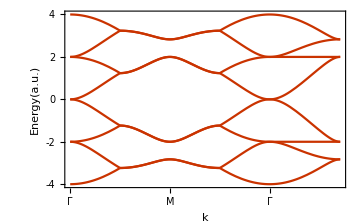

```mathematica
Show[%103,ImageSize->Medium]
```

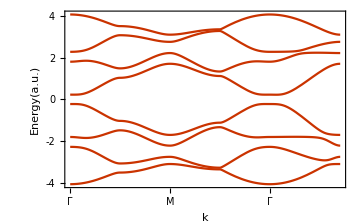

```mathematica
Show[%77,ImageSize->Medium]
```

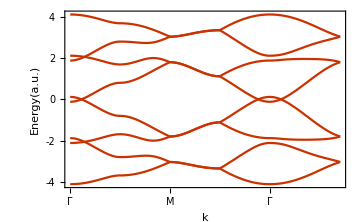

```mathematica
Show[%51,ImageSize->Medium]
```

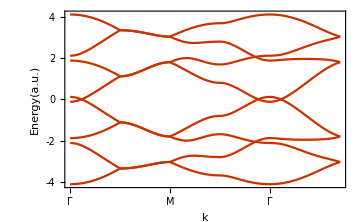

```mathematica
Show[%25,ImageSize->Medium]
```